{0==iR[t]+iZD[t],iR[t]==iC[t]+iR2[t],iR[t]==(u1[t]-u2[t])/10000,iC[t]==u2'[t]/100000000,u1[t]==12.5 Sin[1.2+100000 t],u2[0]==0,iR2[t]==u2[t]/10000}

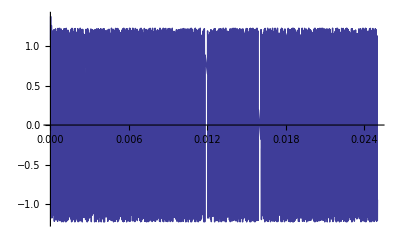

```mathematica
uzel1=0==iZD[t]+iR[t];
uzel2=iR[t]==iC[t]+iR2[t];
odpor=iR[t]==(u1[t]-u2[t])/R;
cond=iC[t]==c*u2'[t];
zdroj=u1[t]==uZ[t];
odpor2=iR2[t]==u2[t]/R2;
podminka=u2[0]==0;

R=10000;
R2=10000;
c=10^-8;
uZ[t_]:=12.5*Sin[10^5*t+1.2];
VsechnyRovnice={uzel1,uzel2,odpor,cond,zdroj,podminka,odpor2}
Reseni=NDSolve[VsechnyRovnice,{iC[t],iZD[t],iR[t],u1[t],u2[t],iR2[t]},{t,0.00001,0.25},MaxSteps-> 1000000];

Plot[u2[t]/.Reseni,{t,0.0000100,0.025}]
```